```mathematica
ClearAll["Global`*"];
```

```mathematica
radiation=11;
blackhole=3;
data={{1,1},{2,1}};
For[j=2,j<=radiation,j++,
k=Prime[j];
c=SparseArray[RandomVariate[NormalDistribution[0,1],{k,blackhole}]];
eigen=IdentityMatrix[blackhole];
radstate=IdentityMatrix[k];
ψ[i_]:=Module[{s},
s=Sum[c[[i]][[a]]*eigen[[a]],{a,1,blackhole}];
Return[s/(√Abs[ConjugateTranspose[s].s])];
];
ρR=1/k Sum[Transpose[{radstate[[j]]}].Conjugate[{radstate[[i]]}]*(ConjugateTranspose[ψ[i]].ψ[j]),{i,1,k},{j,1,k}];
Akk[a1_,a2_]:=SparseArray[Sum[ⅇ^(ⅈ×2π×(a2×(λ-λP))/k)*KroneckerDelta[Mod[2×a1,k],Mod[λ+λP,k]]*Transpose[{radstate[[λ+1]]}].Conjugate[{radstate[[λP+1]]}],{λ,0,k-1},{λP,0,k-1}]];
wsykenkk[x_,y_]:=1/k Chop[Tr[Akk[Mod[x,k],Mod[y,k]].ρR]];
Neg=Chop[ParallelSum[Abs[wsykenkk[x,y]],{x,0,k-1},{y,0,k-1}]];
AppendTo[data,{k,Neg}];

];//AbsoluteTiming
```

{1023.09,Null}

```mathematica
data
```

{{1,1},{2,1},{3,1.04453},{5,1.48118},{7,1.50841},{11,1.72773},{13,1.78555},{17,1.95599},{19,2.09543},{23,2.3067},{29,2.68074},{31,2.66563}}

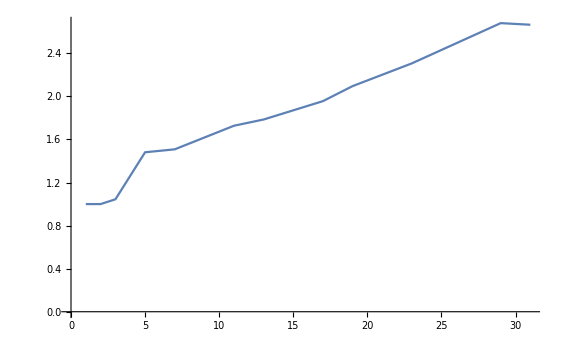

```mathematica
ListPlot[data,Joined->True]
```

```mathematica
Prime[49]
```

227

```mathematica
Plot3D[{-2 x^2 y,-2y},{x,-10,10},{y,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
ρR
```

{{0.177367,-0.0150538,-0.112813},{-0.0150538,2.24322,0.878585},{-0.112813,0.878585,0.408642}}

```mathematica
k=3;
c=SparseArray[RandomVariate[NormalDistribution[0,1],{k,blackhole}]];
eigen=IdentityMatrix[blackhole];
radstate=IdentityMatrix[k];
ψ[i_]:=Sum[c[[i]][[a]]*eigen[[a]],{a,1,blackhole}];
```

```mathematica
ψ[1]
```

{-0.337312,1.21958,-2.06419}

```mathematica
Transpose[{radstate[[1]]}].Conjugate[{radstate[[2]]}]
```

{{0,1,0},{0,0,0},{0,0,0}}

```mathematica
c=SparseArray[RandomVariate[NormalDistribution[0,1],{3,3}]];
```

```mathematica
c//MatrixForm
```

(1.40203 | -1.53417 | -0.278165
0.125001 | -1.19822 | -0.0409872
-0.836639 | -0.861166 | 1.07475)

```mathematica
Normal
```

```mathematica
Prime[17]
```

59

```mathematica
F[rrr_,r_]:=Module[{s},s=If[0<t<=π/2,ArcTan[√(1+rrr^2)Tan[r]/(√(rrr^2-Tan[r]^2))],-ArcTan[√(1+rrr^2)Tan[r]/(√(rrr^2-Tan[r]^2))]];Return[s];];
```

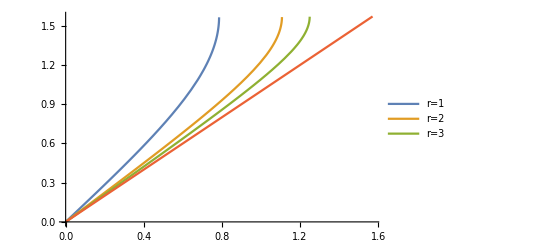

```mathematica
Plot[{F[1,t],F[2,t],F[3,t],t},{t,0,π/2},PlotLegends->{"r=1","r=2","r=3"}]
```

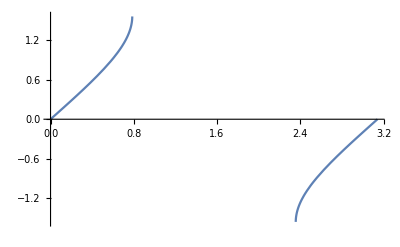

```mathematica
Plot[ArcTan[√2 Tan[r]/(√(1-Tan[r]^2))],{r,0,π}]
```